```mathematica
ϕ=GoldenRatio//N;
Ψ=1-ϕ//N;
θ=Exp[I*Pi*2/5];
```

```mathematica
Fat[{a_,b_,c_}]:={{a,b,c},"fat"};
Skinny[{a_,b_,c_}]:={{a,b,c},"skinny"};
Coor:=Transpose[{Re/@#,Im/@#}]&;
Cent[{{a_,b_,c_},f_}]:=(a+b)*0.5;
Conj[{{a_,b_,c_},f_}]:={Conjugate/@{a,b,c},f};
AddConj[list_]:=Union[list,Conj/@list];
Cull[l_]:=DeleteDuplicatesBy[l,Cent];
Rhomb[{{a_,b_,c_},f_}]:={{a,a-c+b,b,c},f};
Δ[{t_,fs_}]:=t;
See:=Graphics[{EdgeForm[Black],Transpose[{Map[If[Last[#]=="fat",Green,Blue]&,#]&@#,Polygon/@Coor/@Δ/@#}]}]&
```

```mathematica
unitfat=Fat[{0,-ϕ,ⅇ^((4 ⅈ π)/5)}];
unitskinny=Fat[{-0.5,0.5,0.5Sqrt[5+2Sqrt[5]]I}];
```

```mathematica
FatInflate[{{a_,b_,c_},f_}]:=
Block[{
d=a+(c-a)/ϕ,
e=a+(b-a)/ϕ},
{Fat[{e,a,d}],Skinny[{d,c,e}],Fat[{b,c,e}]}]

SkinnyInflate[{{a_,b_,c_},s_}]:=
Block[{d=c+(a-c)/ϕ},
{Skinny[{d,a,b}],Fat[{b,c,d}]}]
Inflate:=If[Last[#]=="fat",FatInflate[#],SkinnyInflate[#]]&
```

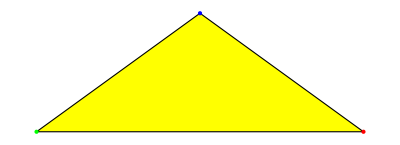

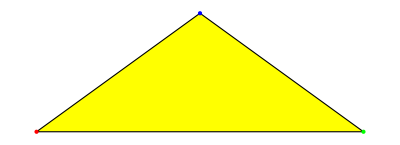
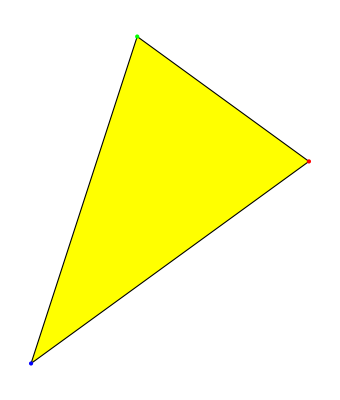
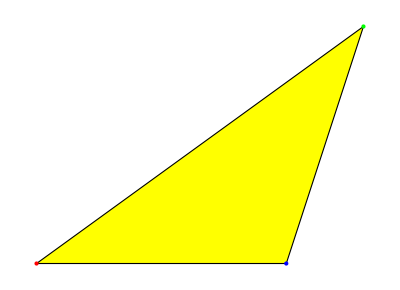

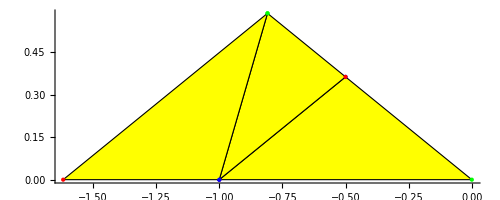

```mathematica
TestPoints@unitfat
TestPoints/@Inflate@unitfat
Show[{TestPoints/@Inflate@unitfat},Axes->True]
```

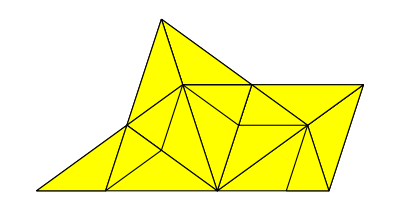

```mathematica
FatInflate/@(Δ/@TriTest);
Δ/@Flatten[%,1];
Coor/@%;
Triangle/@%;
Graphics[{Yellow,EdgeForm[Black],%}]
```

```mathematica
x0=1;
x1=x0*θ;
x2=x1*θ;
y2=-ϕ;
y1=y2/θ;
y0=y1/θ;
TriTest={Fat[{0,y0,x0}],Fat[{0,y0,x1}],Fat[{0,y1,x1}],Fat[{0,y1,x2}],Fat[{0,y2,x2}]};
```

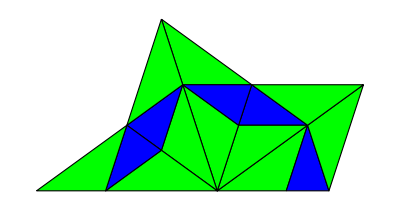

```mathematica
See[Flatten[Inflate/@TriTest,1]]
```

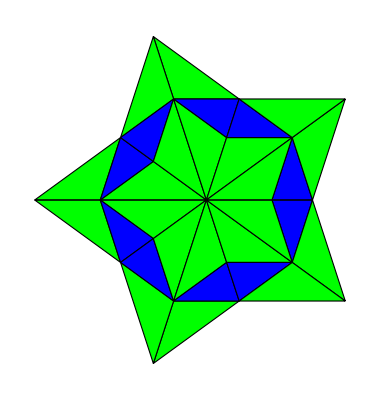

```mathematica
See@AddConj@Flatten[Inflate/@TriTest,1]
```

```mathematica
TestPoints:=Graphics@{Yellow,EdgeForm[Black],{Triangle@Coor@ Δ@#,{PointSize[Large],Transpose[{{Red,Green,Blue},Point/@Coor@Δ@#}]}}}&
```

```mathematica
Inflate[unitfat]
See@Inflate[unitfat]
See@Flatten[Inflate/@Inflate[unitfat],1]
```

```mathematica
Transpose[{Polygon/@Coor/@Δ/@#,Map[If[Last[#]=="fat",Yellow,Blue]&,#]&}]&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

```mathematica
Transpose[{Polygon/@Coor/@Δ/@#&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3],Map[If[Last[#]=="fat",Yellow,Blue]&,#]&}]@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

```mathematica
Transpose[{Map[If[Last[#]=="fat",Yellow,Blue]&,#]&@#,Polygon/@Coor/@Δ/@#&@#}
]&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

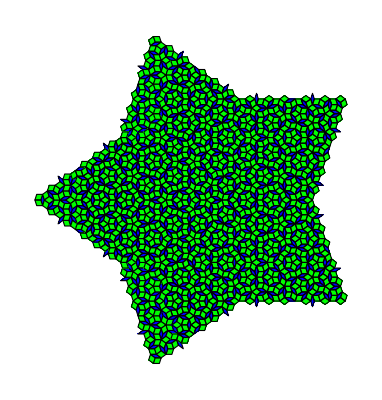

```mathematica
See[Rhomb/@Cull@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,6]]
```

```mathematica
See[Rhomb/@Cull@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,9]]//Timing
```

{1.90121,-Graphics-}

```mathematica
See@%
```

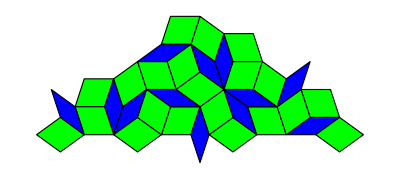

```mathematica
See[Rhomb/@Cull@Nest[Flatten[Inflate/@#,1]&,{unitfat},4]]
```

```mathematica
Graphics[{Yellow,EdgeForm[Black],Polygon/@Coor/@Δ/@#}]&
```

```mathematica
Cull@Nest[Flatten[Inflate/@#,1]&,{unitfat},4]
```

```mathematica
{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}
```

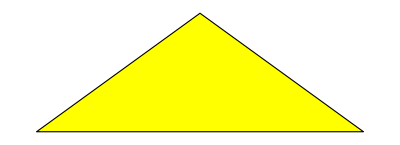

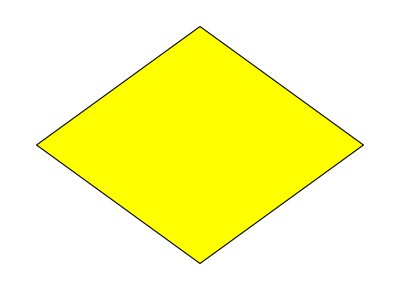

```mathematica
See@{{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}}
See@{Rhomb@{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}}
```

{{0,-1.61803,ⅇ^((4 ⅈ π)/5)},fat}

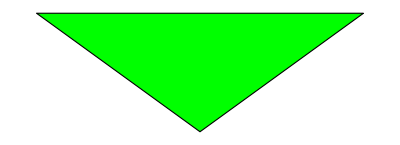

```mathematica
unitfat
See@{Conj[unitfat]}
```

```mathematica
test=Nest[Flatten[Inflate/@#,1]&,TriTest,5];
Sort
```

Sort

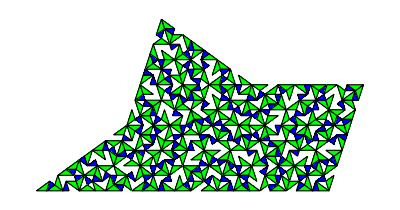
{0.0119,-Graphics-}

```mathematica
See@Cull@test//Timing
```

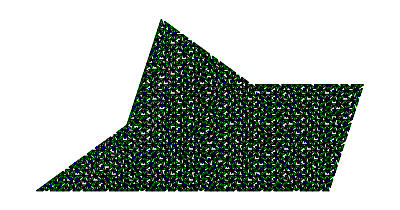
{33.4458,-Graphics-}

```mathematica
See@Cull@SortBy[test,Cent]//Timing
```

```mathematica
See@DeleteDuplicatesBy[test,Cent]
```

-Graphics-